```mathematica
maximalQ[mat1_]:=
Module[{t,mat2},
t=True;
Do[
If[i≠j&&mat1[[i,j]]==0,
mat2=mat1;
mat2[[i,j]]=1;
mat2[[j,i]]=1;
If[MemberQ[primegraphs,mat2],
t=False;
Break[]
]
],
{i,Length[mat1]},{j,i,Length[mat1]}
];
Return[t(*{t,AdjacencyGraph[mat2],MatrixForm[mat2-mat1]}*)];
];


secondmaximal[mat1_]:=
Module[{t,mat2},
t = True;
Do[
If[i≠j&&mat1[[i,j]]==0,
mat2=mat1;
mat2[[i,j]]=1;
mat2[[j,i]]=1;
If[primeGraphQ[mat2],
t=False;
Break[]
]
],
{i,Length[mat1]},{j,i,Length[mat1]}
];
Return[t];
];



primeGraphQ[mat1_]:=
Module[{t,mat2},
t=False;
mat2=MatrixPower[mat1,3];
If[ContainsOnly[Table[mat2[[k,k]],{k,Length[mat1]}],{0}],
If[ChromaticPolynomial[AdjacencyGraph[mat1],3]!=0,
t=True;
]];
Return[t];
];
```

```mathematica
AbsoluteTiming[graphsg=Import["/Users/elistroud/Downloads/graph8c.g6"];]
AbsoluteTiming[graphs=AdjacencyMatrix/@GraphComplement/@graphsg;]
AbsoluteTiming[primegraphs=Parallelize[Select[graphs,primeGraphQ]];]
Length[primegraphs]
```

{4.8938,Null}

{2.92757,Null}

{0.570944,Null}

406

{0.158852,Null}

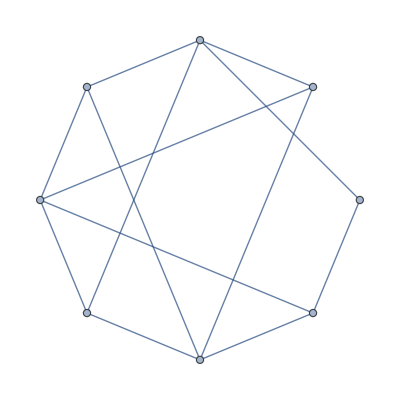
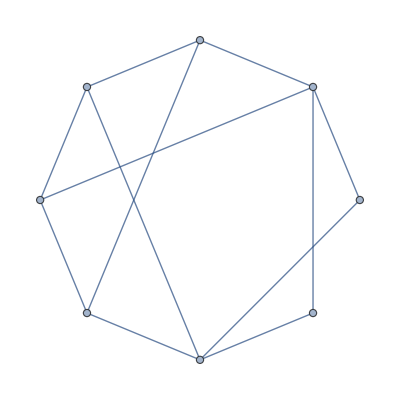
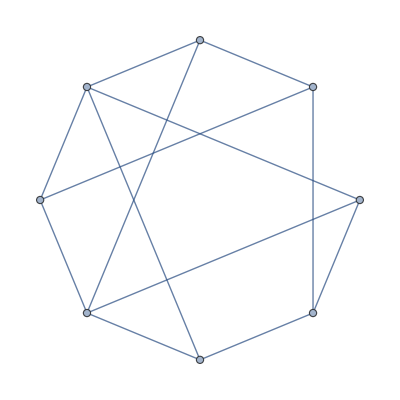
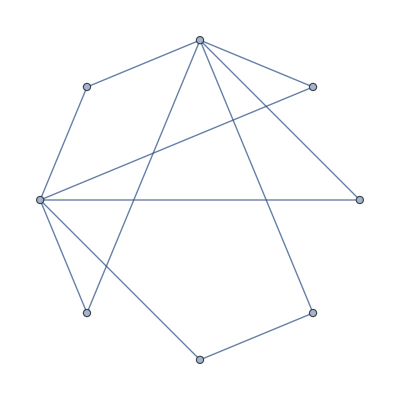
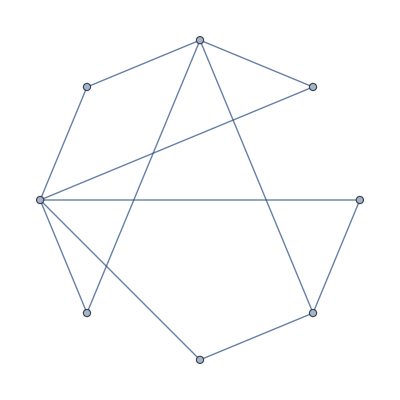
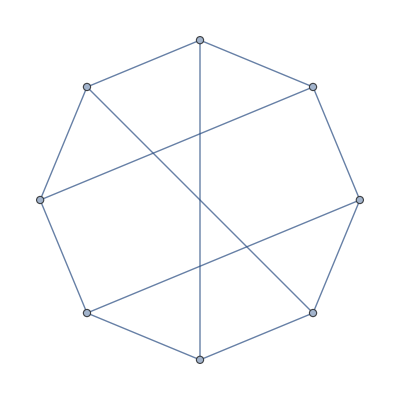

```mathematica
AbsoluteTiming[maximalprimegraphs=Parallelize[Select[primegraphs,secondmaximal]];]
pictures=AdjacencyGraph[#,VertexCoordinates->Table[{Cos[i 2 Pi/8],Sin[i 2 Pi/8]},{i,1,8}]]&/@maximalprimegraphs
```

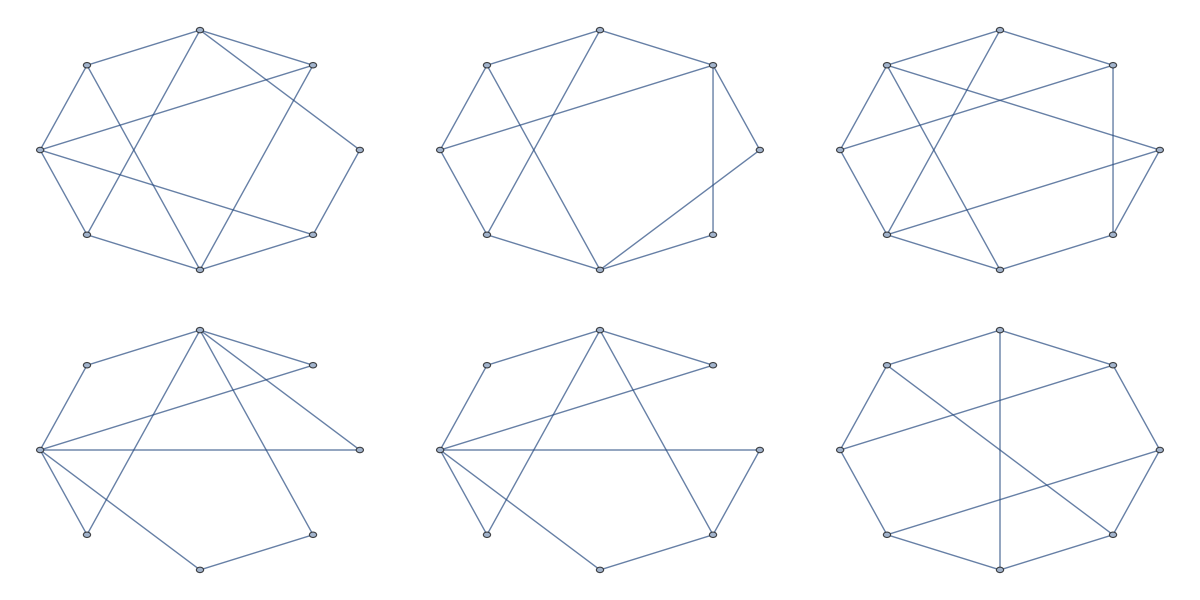

```mathematica
Grid[{pictures[[1;;3]],pictures[[4;;6]]}]
```

```mathematica
Beep[]
```

```mathematica
Export["pictures.jpg",Grid[{pictures[[1;;3]],pictures[[4;;6]]}]]
```

pictures.jpg

```mathematica
Import[%]
```

-Graphics-